```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
Needs["PlotLegends`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar\\runs2"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/analysis-mirror_neutrons/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadesc={Number,Number,Number,Number,Number,Number,Number,Word,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desctf_c.dat"],metadesc];
dimdesc=Dimensions[descdat][[1]];
(*LS-Periodogram*)
LS[tx_, nP_] := 
 LS[tx, nP] = 
  Block[{t, x, xbar, std, τ, P, Ω, diff, lim, 
     periodogram},
    t = Table[tx[[i, 1]], {i, 1, Length[tx]}];
    x = Table[tx[[i, 2]], {i, 1, Length[tx]}];
    xbar = Mean[x];
    std = 1/(Length[x] - 1.) Sum[(x[[i]] - xbar)^2, {i, 1, Length[x]}];
    τ[ω_] := τ[ω] = ArcTan[∑_(i=1)^Length[tx] Sin[2. ω x[[i]]]/∑_(i=1)^Length[tx] Cos[2. ω x[[i]]]]/(2. ω);
    P[ω_] := P[ω] = (0.5/std) ((∑_(i=1)^Length[tx] (x[[i]]-xbar) Cos[ω (t[[i]]-τ[ω])])^2/∑_(i=1)^Length[tx] Cos[ω (t[[i]]-τ[ω])]^2 + (∑_(i=1)^Length[tx] (x[[i]]-xbar) Sin[ω (t[[i]]-τ[ω])])^2/∑_(i=1)^Length[tx] Sin[ω (t[[i]]-τ[ω])]^2);
    Ω[T_] := Ω[T] = 2. π/T;
    diff = Table[t[[i + 1]] - t[[i]], {i, 1, Length[t] - 1}]; 
    lim = Ω /@ {Last[t] - First[t], 2 Min[diff]};
    periodogram = 
     ParallelTable[{ω, P[ω]}, {ω, lim[[1]], 
       lim[[2]], (lim[[2]] - lim[[1]])/nP}]
    ];
LSCos[tx_, nP_] := 
 LSCos[tx, nP] = 
  Block[{t, x, xbar, std, τ, P, Ω, diff, lim, 
     periodogram},
    t = Table[tx[[i, 1]], {i, 1, Length[tx]}];
    x = Table[tx[[i, 2]], {i, 1, Length[tx]}];
    xbar = Mean[x];
    std = 1/(Length[x] - 1.) Sum[(x[[i]] - xbar)^2, {i, 1, Length[x]}];
    τ[ω_] := τ[ω] = ArcTan[∑_(i=1)^Length[tx] Cos[2. ω x[[i]]]/∑_(i=1)^Length[tx] Sin[2. ω x[[i]]]]/(2. ω);
    P[ω_] := P[ω] = (0.5/std) ((∑_(i=1)^Length[tx] (x[[i]]-xbar) Sin[ω (t[[i]]-τ[ω])])^2/∑_(i=1)^Length[tx] Sin[ω (t[[i]]-τ[ω])]^2 + (∑_(i=1)^Length[tx] (x[[i]]-xbar) Cos[ω (t[[i]]-τ[ω])])^2/∑_(i=1)^Length[tx] Cos[ω (t[[i]]-τ[ω])]^2);
    Ω[T_] := Ω[T] = 2. π/T;
    diff = Table[t[[i + 1]] - t[[i]], {i, 1, Length[t] - 1}]; 
    lim = Ω /@ {Last[t] - First[t], 2 Min[diff]};
    periodogram = 
     ParallelTable[{ω, P[ω]}, {ω, lim[[1]], 
       lim[[2]], (lim[[2]] - lim[[1]])/nP}]
    ];
T[periodogram_,rankmax_]:=T[periodogram,rankmax]=Block[{power,ωmax,period},power=Table[periodogram[[i,2]],{i,1,Length[periodogram]}];
ωmax=periodogram[[Position[power,RankedMax[power,rankmax]][[1,1]],1]];
{period=2 π/ωmax,RankedMax[power,rankmax]}];
p[z_,n_]:=p[z,n]=1-(1-Exp[-z])^n;
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Working Directory: C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\runs2

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

## Making lvl3 for Sidereal

```mathematica
rundat={};
starttime=0;
pta10=pta20=fta10=fta20=erra10=erra20=fta102=fta202={};
bpt10=bft10=errb10={};
bpt20=bft20=errb20={};
bpt0=bft0=errb0={};
ptarun=Table[{},{k,1,dimdesc}];ptarun2=Table[{},{k,1,dimdesc}];
ftarun=Table[{},{k,1,dimdesc}];ftarun2=Table[{},{k,1,dimdesc}];
errarun=Table[{},{k,1,dimdesc}];errarun2=Table[{},{k,1,dimdesc}];
tsadd=2*PlusMinus[11.306,0.397];
For[i=1,i≤dimdesc,i++,
pmb0run=pmbbrun={};
If[(descdat[[i]][[5]]>20&&descdat[[i]][[5]]<9000(*&&MemberQ[{1,2,3,4,5,39,40,41},i]*))
,
(*Print[descdat[[i]][[4]]];*)
rundat=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl2.dat"],{Real,Real,Real,Real,Real,Real,Real,Real,Real}];
dimrundat=Dimensions[rundat][[1]];
If[i==1,starttime=rundat[[1]][[1]]];
(*For-A*tf/ts*)
ptarun[[i]]=Table[
{
Mod[(rundat[[;;,1]][[k]]-starttime)/(86164.09054),1],
0.1*{
((PlusMinus[rundat[[;;,{2,3}]][[k]][[1]],rundat[[;;,{2,3}]][[k]][[2]]])*10^6*((PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]])/(PlusMinus[descdat[[i]][[7]],0.1]+tsadd)))[[1]],
Abs[((PlusMinus[rundat[[;;,{2,3}]][[k]][[1]],rundat[[;;,{2,3}]][[k]][[2]]])*10^6*((PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]])/(PlusMinus[descdat[[i]][[7]],0.1]+tsadd)))[[2]]]
}
},
{k,1,Dimensions[rundat[[;;,{2,3}]]][[1]]}
];
ftarun[[i]]=Transpose[{ptarun[[i]][[;;,1]],ptarun[[i]][[;;,2]][[;;,1]]}];
errarun[[i]]=Abs[ptarun[[i]][[;;,2]][[;;,2]]];
(*For-A*)
ptarun2[[i]]=Table[{Mod[(rundat[[;;,1]][[k]]-starttime)/(86164.09054),1],{rundat[[;;,{2,3}]][[k]][[1]],Abs[rundat[[;;,{2,3}]][[k]][[2]]]}},{k,1,Dimensions[rundat[[;;,{2,3}]]][[1]]}];
ftarun2[[i]]=Transpose[{ptarun2[[i]][[;;,1]],ptarun2[[i]][[;;,2]][[;;,1]]}];
errarun2[[i]]=Abs[ptarun2[[i]][[;;,2]][[;;,2]]];
(**)
If[descdat[[i]][[6]]==10,
{
bpt10=Join[bpt10,Transpose[{Mod[(rundat[[;;,1]]-starttime)/(86164.09054),1],rundat[[;;,{8,9}]]}]];
bft10=Join[bft10,Transpose[{Mod[(rundat[[;;,1]]-starttime)/(86164.09054),1],rundat[[;;,8]]}]];
errb10=Join[errb10,rundat[[;;,9]]];
pmbbrun=Join[pmbbrun,Table[PlusMinus[rundat[[k]][[8]],rundat[[k]][[9]]],{k,1,dimrundat}]];
(*A*)
pta10=Join[pta10,ptarun[[i]]];
fta10=Join[fta10,ftarun[[i]]];
erra10=Join[erra10,errarun[[i]]];
},
{
bpt20=Join[bpt20,Transpose[{Mod[(rundat[[;;,1]]-starttime)/(86164.09054),1],rundat[[;;,{8,9}]]}]];
bft20=Join[bft20,Transpose[{Mod[(rundat[[;;,1]]-starttime)/(86164.09054),1],rundat[[;;,8]]}]];
errb20=Join[errb20,rundat[[;;,9]]];
pmbbrun=Join[pmbbrun,Table[PlusMinus[rundat[[k]][[8]],rundat[[k]][[9]]],{k,1,dimrundat}]];
(*A*)
pta20=Join[pta20,ptarun[[i]]];
fta20=Join[fta20,ftarun[[i]]];
erra20=Join[erra20,errarun[[i]]];
}
];
bpt0=Join[bpt0,Transpose[{Mod[(rundat[[;;,1]]-starttime)/(86164.09054),1],rundat[[;;,{6,7}]]}]];
bft0=Join[bft0,Transpose[{Mod[(rundat[[;;,1]]-starttime)/(86164.09054),1],rundat[[;;,6]]}]];
errb0=Join[errb0,rundat[[;;,7]]];
];
lvl3={{}};
(*Export[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3sidereal.dat"],lvl3];*)
];
```

## Do Not Run: Individual Run-Combined-Fit

```mathematica
fitsize=dimdesc;
StringDrop[StringJoin[Table[StringJoin["MDL==",ToString[k],",Evaluate@model[[",ToString[k],"]],"],{k,1,fitsize}]],-1]
```

MDL==1,Evaluate@model[[1]],MDL==2,Evaluate@model[[2]],MDL==3,Evaluate@model[[3]],MDL==4,Evaluate@model[[4]],MDL==5,Evaluate@model[[5]],MDL==6,Evaluate@model[[6]],MDL==7,Evaluate@model[[7]],MDL==8,Evaluate@model[[8]],MDL==9,Evaluate@model[[9]],MDL==10,Evaluate@model[[10]],MDL==11,Evaluate@model[[11]],MDL==12,Evaluate@model[[12]],MDL==13,Evaluate@model[[13]],MDL==14,Evaluate@model[[14]],MDL==15,Evaluate@model[[15]],MDL==16,Evaluate@model[[16]],MDL==17,Evaluate@model[[17]],MDL==18,Evaluate@model[[18]],MDL==19,Evaluate@model[[19]],MDL==20,Evaluate@model[[20]],MDL==21,Evaluate@model[[21]],MDL==22,Evaluate@model[[22]],MDL==23,Evaluate@model[[23]],MDL==24,Evaluate@model[[24]],MDL==25,Evaluate@model[[25]],MDL==26,Evaluate@model[[26]],MDL==27,Evaluate@model[[27]],MDL==28,Evaluate@model[[28]],MDL==29,Evaluate@model[[29]],MDL==30,Evaluate@model[[30]],MDL==31,Evaluate@model[[31]],MDL==32,Evaluate@model[[32]],MDL==33,Evaluate@model[[33]],MDL==34,Evaluate@model[[34]],MDL==35,Evaluate@model[[35]],MDL==36,Evaluate@model[[36]]

```mathematica
Clear[aa,bb,MDL];
tabdesc=Table[k,{k,1,fitsize}];
combidata=Flatten[Table[Insert[#,k,2]&/@ftarun2[[k]],{k,1,fitsize}],1];
combierr=Flatten[Join[errarun2],1];
Dimensions[combidata][[1]];
Dimensions[combierr][[1]];
aa=Symbol["a"<>ToString[#]]&/@Range[fitsize];
bb=Symbol["b"<>ToString[#]]&/@Range[fitsize];
model=Table[aa [[k]]Cos[2Pi ( t + phi)]+bb[[k]],{k,1,fitsize}];
combimodel:=Which[MDL==1,Evaluate@model[[1]],MDL==2,Evaluate@model[[2]],MDL==3,Evaluate@model[[3]],MDL==4,Evaluate@model[[4]],MDL==5,Evaluate@model[[5]],MDL==6,Evaluate@model[[6]],MDL==7,Evaluate@model[[7]],MDL==8,Evaluate@model[[8]],MDL==9,Evaluate@model[[9]],MDL==10,Evaluate@model[[10]],MDL==11,Evaluate@model[[11]],MDL==12,Evaluate@model[[12]],MDL==13,Evaluate@model[[13]],MDL==14,Evaluate@model[[14]],MDL==15,Evaluate@model[[15]],MDL==16,Evaluate@model[[16]],MDL==17,Evaluate@model[[17]],MDL==18,Evaluate@model[[18]],MDL==19,Evaluate@model[[19]],MDL==20,Evaluate@model[[20]],MDL==21,Evaluate@model[[21]],MDL==22,Evaluate@model[[22]],MDL==23,Evaluate@model[[23]],MDL==24,Evaluate@model[[24]],MDL==25,Evaluate@model[[25]],MDL==26,Evaluate@model[[26]],MDL==27,Evaluate@model[[27]],MDL==28,Evaluate@model[[28]],MDL==29,Evaluate@model[[29]],MDL==30,Evaluate@model[[30]],MDL==31,Evaluate@model[[31]],MDL==32,Evaluate@model[[32]],MDL==33,Evaluate@model[[33]],MDL==34,Evaluate@model[[34]],MDL==35,Evaluate@mode.l[[35]],MDL==36,Evaluate@model[[36]],True,0];
Flatten[{aa,bb,phi}]
nlmreport=Quiet[NonlinearModelFit[combidata,{combimodel,(aa>0&&aa<0.01&&bb>-0.01&&bb<0.01&&phi>-1/2&&phi<1/2)},Flatten[{aa,bb,phi}],{t,MDL},Method->NMinimize,ConfidenceLevel->.95]];
wrtsidereal=Quiet[nlmreport["ParameterTable"]]
```

{a1,a2,a3,a4,a5,a6,a7,a8,a9,0.00082±0.00072,0.00042±0.00051,-0.00072±0.00042,-0.00051±0.00082,0.00098±0.00064,a11,a12,a13,a14,a15,a16,a17,a18,a19,0.00039±0.00077,0.00033±0.00077,-0.00045±0.00038,a21,a22,a23,a24,a25,a26,a27,a28,a29,a30,a31,a32,a33,a34,a35,a36,b1,b2,b3,b4,b5,b6,b7,b8,b9,0.0101944±5.8×10^-6,0.0101942±3.6×10^-6,0.0101958±2.2×10^-6,0.010196±2.6×10^-6,0.0101965±8.5×10^-8,b11,b12,b13,b14,b15,b16,b17,b18,b19,0.0203864±1.4×10^-7,0.0203869±2.3×10^-7,0.0203869±1.1×10^-7,b21,b22,b23,b24,b25,b26,b27,b28,b29,b30,b31,b32,b33,b34,b35,b36,phi}

NMinimize::bcons: The following constraints are not valid: {a1>0,a11>0,a12>0,a13>0,a14>0,a15>0,a16>0,a17>0,a18>0,a19>0,a2>0,a21>0,a22>0,a23>0,a24>0,a25>0,a26>0,a27>0,a28>0,a29>0,a3>0,a30>0,a31>0,a32>0,a33>0,a34>0,a35>0,a36>0,a4>0,a5>0,a6>0,a7>0,a8>0,a9>0,b1>-0.01,b11>-0.01,b12>-0.01,b13>-0.01,b14>-0.01,b15>-0.01,b16>-0.01,b17>-0.01,b18>-0.01,b19>-0.01,b2>-0.01,b21>-0.01,b22>-0.01,b23>-0.01,b24>-0.01,b25>-0.01,«96»}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

$Aborted

$Aborted

```mathematica
dimdesc
wrtsidereal[[1]][[1]][[1+1]]
wrtsidereal[[1]][[1]][[1+dimdesc+1]]
wrtsidereal[[1]][[1]][[-1]]
{wrtsidereal[[1]][[1]][[1+1]][[2]],wrtsidereal[[1]][[1]][[1+1]][[3]],wrtsidereal[[1]][[1]][[1+dimdesc+1]][[2]],wrtsidereal[[1]][[1]][[1+dimdesc+1]][[3]],wrtsidereal[[1]][[1]][[-1]][[2]],wrtsidereal[[1]][[1]][[-1]][[3]]}
```

36

{a1,0.,0.00857238,0.,1.}

{b1,0.00181987,0.00553084,0.329041,0.742954}

{phi,-0.335371,0.117691,-2.84958,0.00551937}

{0.,0.00857238,0.00181987,0.00553084,-0.335371,0.117691}

```mathematica
(*Write to file: a sin (Ω(t + ϕ)); {a, Subscript[σ, a], b, Subscript[σ, b], ϕ, Subscript[σ, ϕ]} *)
For[i=1,i≤dimdesc,i++,
If[(descdat[[i]][[5]]>1&&descdat[[i]][[5]]<9000)
,
lvl3={{wrtsidereal[[1]][[1]][[1+i]][[2]],wrtsidereal[[1]][[1]][[1+i]][[3]],wrtsidereal[[1]][[1]][[1+dimdesc+i]][[2]],wrtsidereal[[1]][[1]][[1+dimdesc+i]][[3]],wrtsidereal[[1]][[1]][[-1]][[2]],wrtsidereal[[1]][[1]][[-1]][[3]]}};
(*Print[descdat[[i]][[4]]];*)
Export[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3sidereal.dat"],lvl3];
]
]
```

## Combined Fit {10,20}μT

χ^2 {10,20}μT : { 6.21406 , 18.6679 }

| Estimate | Standard Error | t-Statistic | P-Value
a1 | 0.0293204 | 0.0234428 | 1.25072 | 0.214014
b1 | -0.0354163 | 0.0195475 | -1.8118 | 0.0730792
b2 | -0.00513934 | 0.0339838 | -0.151229 | 0.880106
phi | 0.157274 | 0.131914 | 1.19224 | 0.236045

{0.0293204,-0.0354163,-0.00513934,0.157274}

{0.0234428,0.0195475,0.0339838,0.131914}

{1.25072,-1.8118,-0.151229,1.19224}

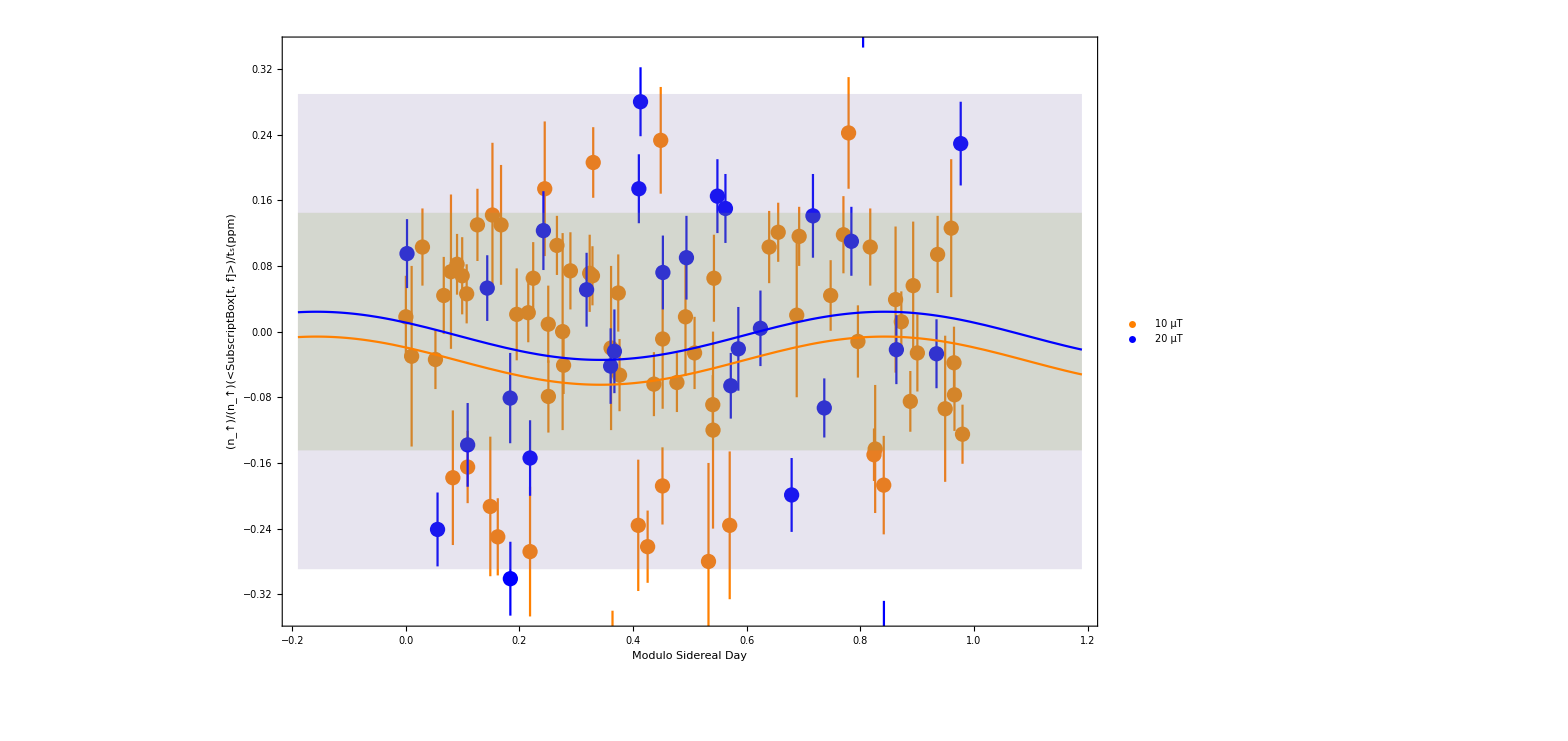

```mathematica
Clear[aa,bb,MDL];
cutoff=3;
cleanpta10=Select[pta10,Abs[#[[2]][[1]]]<cutoff&];
cleanpta20=Select[pta20,Abs[#[[2]][[1]]]<cutoff*1.5&];
cleanfta10=Table[{cleanpta10[[k]][[1]],cleanpta10[[k]][[2]][[1]]},{k,1,Dimensions[cleanpta10][[1]]}];
cleanerra10=Table[cleanpta10[[k]][[2]][[2]],{k,1,Dimensions[cleanpta10][[1]]}];
cleanfta20=Table[{cleanpta20[[k]][[1]],cleanpta20[[k]][[2]][[1]]},{k,1,Dimensions[cleanpta20][[1]]}];
cleanerra20=Table[cleanpta20[[k]][[2]][[2]],{k,1,Dimensions[cleanpta20][[1]]}];
(***)
CombiledData=Join[Insert[#,1,2]&/@cleanfta10,Insert[#,2,2]&/@cleanfta20];
Model1=a1 Cos[2Pi( t + phi)]+b1;
Model2=a1 Cos[2Pi( t+ phi)]+b2;
CombinedModel:=Which[MDL==1,Evaluate@Model1,MDL==2,Evaluate@Model2,True,0];
regreport=Quiet[NonlinearModelFit[CombiledData,
{CombinedModel,(a1>0&&a1<10^(2)&&b1>-5*10^(2)&&b1<5*10^(0)&&b2>-5*10^(0)&&b2<5*10^(0)&&phi>-1/2&&phi<1/2)},
{{a1,0.0001},{b1,0.0001},{b2,0.0001},{phi,0}},{t,MDL},Weights->Join[cleanerra10,cleanerra20],Method->NMinimize]];
Print["χ^2 {10,20}μT : { ",
N[Total[Table[((cleanfta10[[k]][[2]]-regreport[cleanfta10[[k]][[1]],1])/cleanerra10[[k]])^2,{k,1,Dimensions[cleanerra10][[1]]}]]/Dimensions[cleanerra10][[1]]]," , ",
N[Total[Table[((cleanfta20[[k]][[2]]-regreport[cleanfta20[[k]][[1]],2])/cleanerra20[[k]])^2,{k,1,Dimensions[cleanerra20][[1]]}]]/Dimensions[cleanerra20][[1]]]," }"]; 
Quiet[regreport["ParameterTable"]]
Quiet[regreport["BestFitParameters"][[;;,2]]]
Quiet[regreport["ParameterErrors"]]
Quiet[regreport["BestFitParameters"][[;;,2]]]/Quiet[regreport["ParameterErrors"]]
(***)
residual=Table[{CombiledData[[k]][[1]],regreport["FitResiduals"][[k]]},{k,1,Dimensions[CombiledData][[1]]}];
residuals=Table[{CombiledData[[k]][[1]],regreport["FitResiduals"][[k]]/Join[cleanerra10,cleanerra20][[k]]},{k,1,Dimensions[CombiledData][[1]]}];
sdcleanpta10=StandardDeviation[cleanpta10[[;;,2]][[;;,1]]];
mnpt=Show[{
EDAListPlot[cleanpta10,cleanpta20,PlotLegends->{"10 μT","20 μT"},PlotRange->{{-.19,1.19},.115{-cutoff,cutoff}},PlotStyle->{Orange,Blue},Frame->True,FrameLabel->{"Modulo Sidereal Day","(n_↑)/(n_↑)(<SubscriptBox[t, f]>)/t_s(ppm)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004]],
Plot[{regreport[t,1],regreport[t,2],sdcleanpta10,-sdcleanpta10,2sdcleanpta10,-2sdcleanpta10},{t,-.19,1.19},PlotStyle->{Orange,Blue,None,None,None,None},Filling->{{3->{4}},{5->{6}}}]
},ImageSize->1200,Frame->{True,True,True,True}]
(*Export[StringJoin[descDir,seperator,"all_lvl3sidereal.dat"],regreport["ParameterTable"][[1]][[1]][[2;;]]];*)
```

```mathematica
regreport["ParameterTable"][[1]][[1]][[2;;]]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{a1,0.104546,0.202801,0.515509,0.607395},{b1,-0.179417,0.170303,-1.05352,0.294777},{b2,0.0945746,0.295763,0.319765,0.749849},{phi,0.085153,0.324928,0.262067,0.793837}}

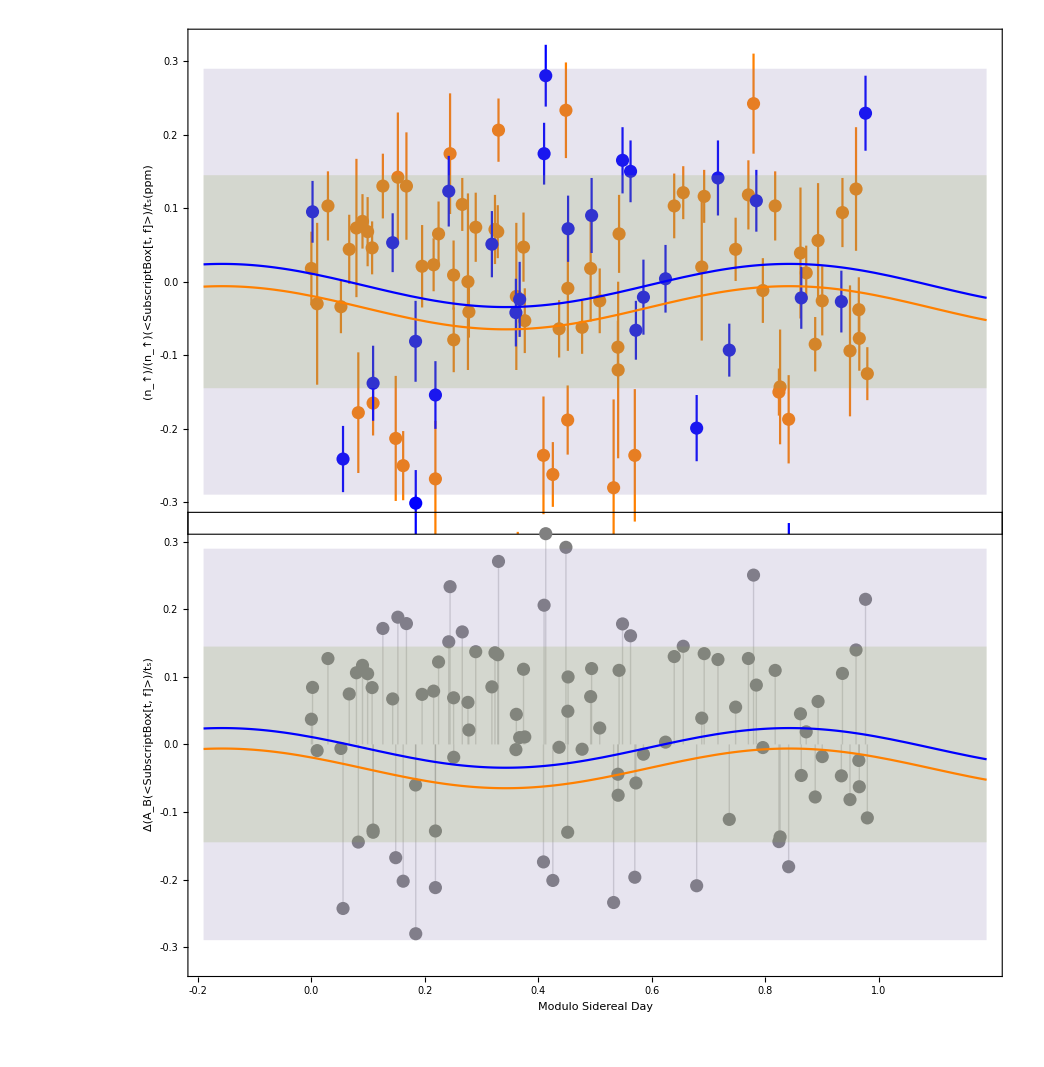

```mathematica
GraphicsGrid[{{
Show[{
EDAListPlot[cleanpta10,cleanpta20,PlotLegend->{"10 μT","20 μT"},PlotRange->{{-.19,1.19},.11{-cutoff,cutoff}},PlotStyle->{Orange,Blue},Frame->True,FrameLabel->{"","(n_↑)/(n_↑)(<SubscriptBox[t, f]>)/t_s(ppm)"},FrameTicks->{{LinTicks,LinTicks},{None,LinTicks}},TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004]],
Plot[{regreport[t,1],regreport[t,2],sdcleanpta10,-sdcleanpta10,2sdcleanpta10,-2sdcleanpta10},{t,-.19,1.19},PlotStyle->{Orange,Blue,None,None,None,None},Filling->{{3->{4}},{5->{6}}},ImagePadding->{{Automatic,None},{Automatic,Automatic}}]},ImageSize->1032
]},{
Show[{ListPlot[residual,PlotRange->{{-.19,1.19},.11{-cutoff,cutoff}},PlotStyle->{Gray},Filling->Axis,FrameLabel->{"Modulo Sidereal Day",Style["Δ(A_B(<SubscriptBox[t, f]>)/t_s)",Black]},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->1032,Frame->{True,True,False,True}],
Plot[{regreport[t,1],regreport[t,2],sdcleanpta10,-sdcleanpta10,2sdcleanpta10,-2sdcleanpta10},{t,-.19,1.19},PlotStyle->{Orange,Blue,None,None,None,None},Filling->{{3->{4}},{5->{6}}},ImagePadding->{{Automatic,None},{Automatic,Automatic}}]},ImageSize->1032]
}},Spacings->{0,-110}]
```

## Power Spectra of A.Cos

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::nopar will be suppressed during this calculation.

{1065.23,Null}

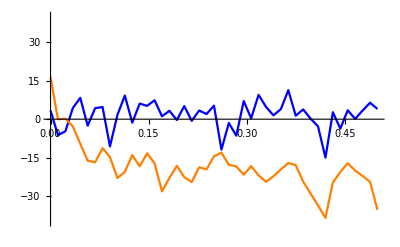

```mathematica
(***MC***)
mcruns=30;
np=1000;
gramftamc=Table[{},{k,1,mcruns}];
gramftamc2=Table[{},{k,1,mcruns}];
(*10*)
totdat=Join[cleanpta10,cleanpta20];
totdatft=Join[cleanfta10,cleanfta20];
Parallelize[
For[j=1,j≤mcruns,j++,
cleanftamc={};
For[i=1,i≤Dimensions[totdat][[1]],i++,
RandomSeed[CurrentDate[]];
cleanftamc=AppendTo[cleanftamc,{totdat[[i]][[1]],RandomVariate[NormalDistribution[totdat[[i]][[2]][[1]],totdat[[i]][[2]][[2]]]]}];
];
gramftamc[[j]]=LS[cleanftamc,np];
gramftamc2[[j]]=LSCos[cleanftamc,np];
];
gramfta=LS[totdatft,np];
gramfta2=LSCos[totdatft,np];
gramftamcm=Mean[gramftamc];
gramftamcm2=Mean[gramftamc2];
gramftamcs=StandardDeviation[gramftamc];
gramftamcs2=StandardDeviation[gramftamc2];
]//AbsoluteTiming
Show[{Periodogram[cleanftamc[[;;,2]],PlotRange->Full,PlotStyle->Blue],
Periodogram[totdat[[;;,2]][[;;,2]],PlotRange->Full,PlotStyle->Orange]
},PlotRange->{{0,.5},{-40,40}}]
```

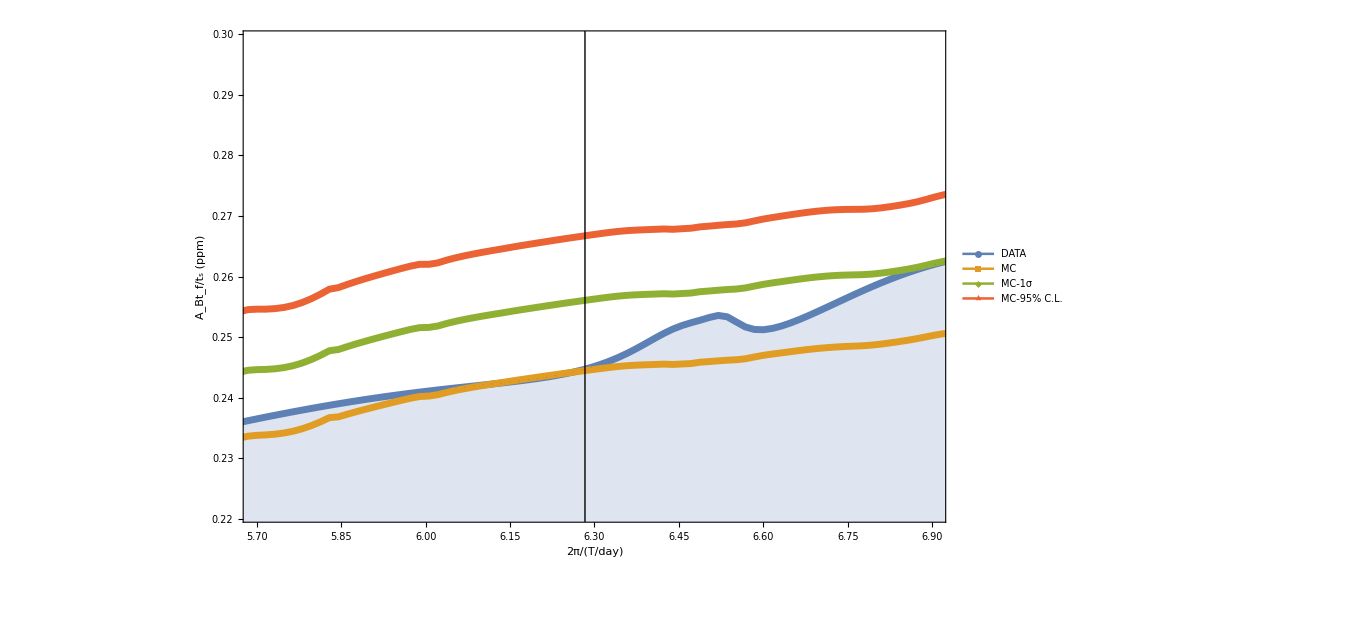

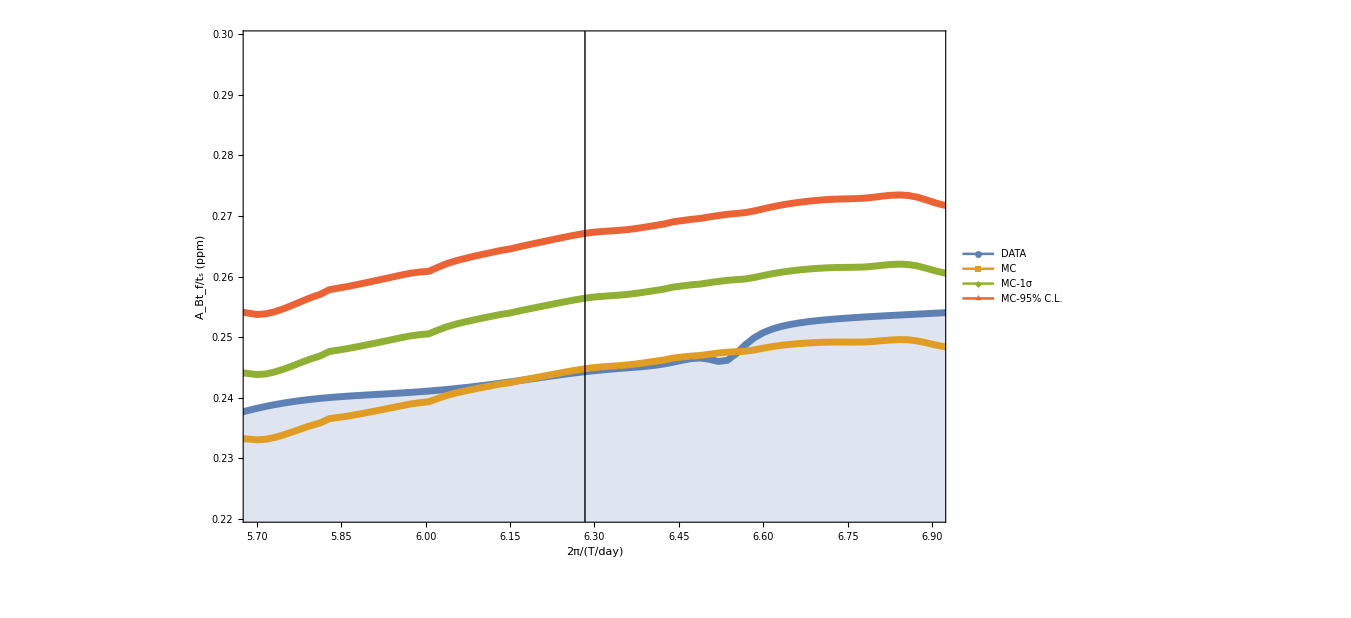

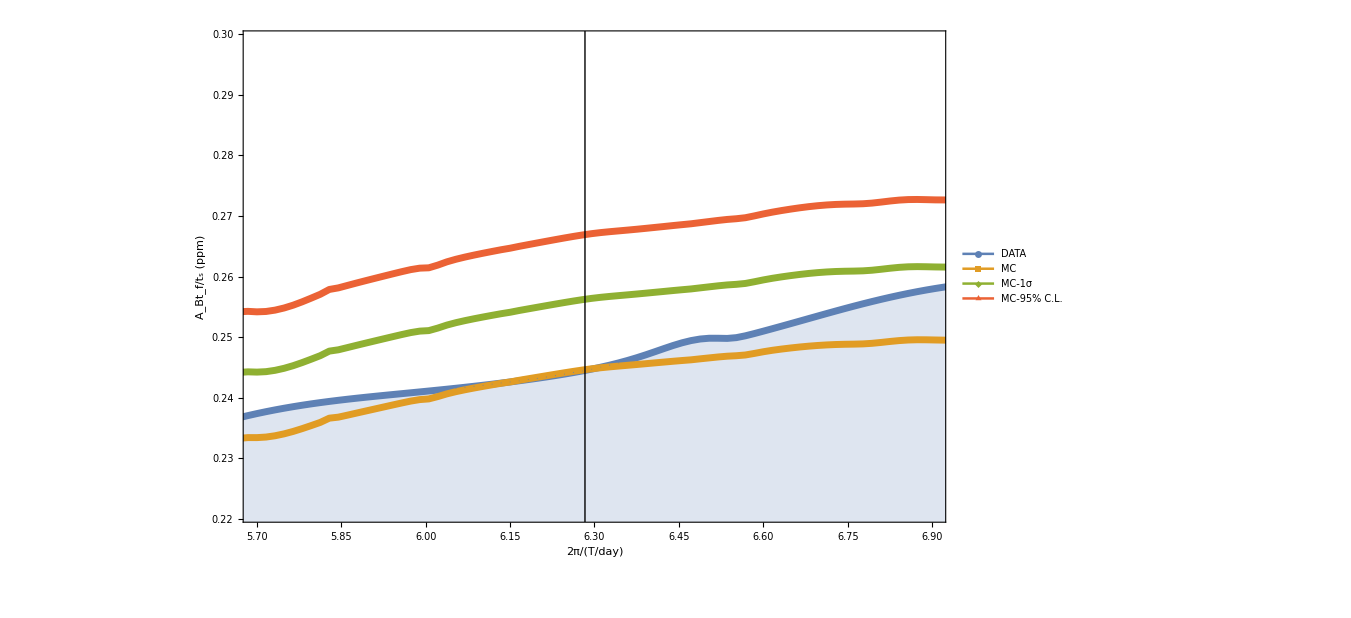

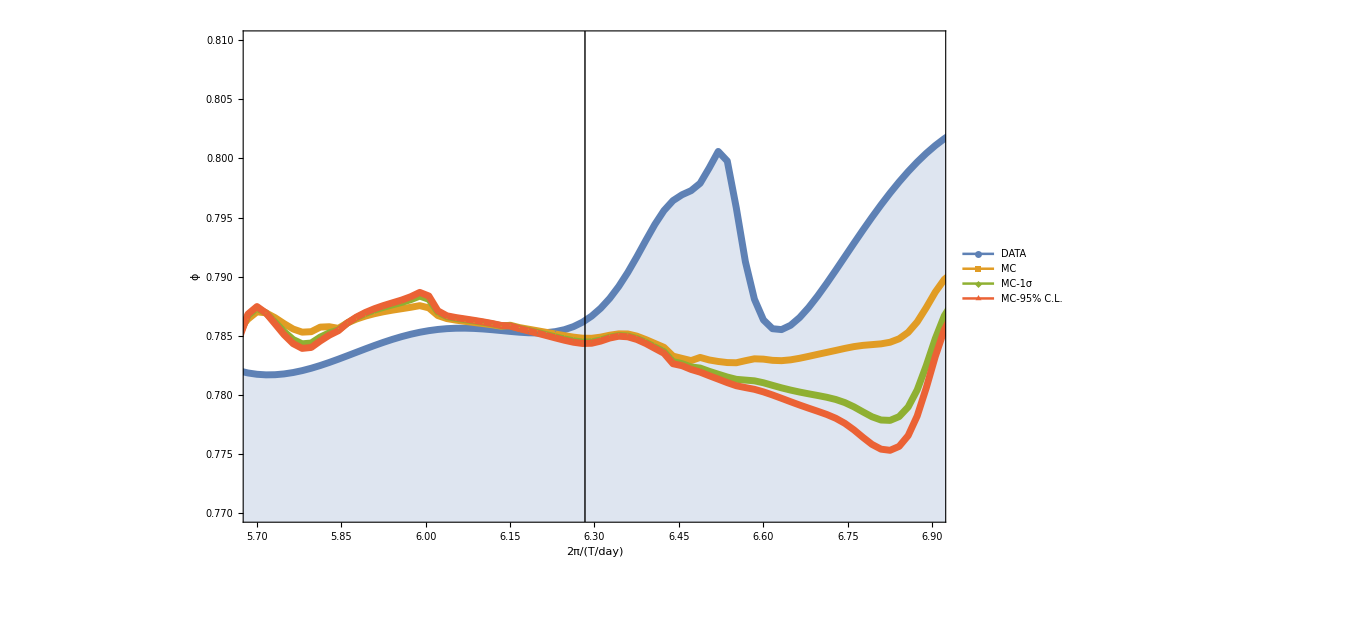

```mathematica
lineStyle={Thick,Black};
ln1=Line[{{ 2Pi,0},{2 Pi,3}}];
ptgramfta=Transpose[{gramfta[[;;,1]],Sqrt[gramfta[[;;,2]]/(4Pi)]}];
ptgramftamcm=Transpose[{gramftamcm[[;;,1]],Sqrt[gramftamcm[[;;,2]]/(4Pi)]}];
ptgramftamcm1=Transpose[{gramfta[[;;,1]],Sqrt[(gramftamcm[[;;,2]]+gramftamcs[[;;,2]]/Sqrt[2 mcruns])/(4Pi)]}];
ptgramftamcm95=Transpose[{gramfta[[;;,1]],Sqrt[(gramftamcm[[;;,2]]+1.96 gramftamcs[[;;,2]]/Sqrt[2 mcruns])/(4Pi)]}];
ptgramfta2=Transpose[{gramfta2[[;;,1]],Sqrt[gramfta2[[;;,2]]/(4Pi)]}];
ptgramftamcm2=Transpose[{gramftamcm2[[;;,1]],Sqrt[gramftamcm2[[;;,2]]/(4Pi)]}];
ptgramftamcm12=Transpose[{gramfta2[[;;,1]],Sqrt[(gramftamcm2[[;;,2]]+gramftamcs2[[;;,2]]/Sqrt[2 mcruns])/(4Pi)]}];
ptgramftamcm952=Transpose[{gramfta2[[;;,1]],Sqrt[(gramftamcm2[[;;,2]]+1.96 gramftamcs2[[;;,2]]/Sqrt[2 mcruns])/(4Pi)]}];
ptgramftap=Transpose[{gramfta2[[;;,1]],ArcTan[Sqrt[gramfta[[;;,2]]/gramfta2[[;;,2]]]]}];
ptgramftamcmp=Transpose[{gramftamcm2[[;;,1]],ArcTan[Sqrt[gramftamcm[[;;,2]]/gramftamcm2[[;;,2]]]]}];
ptgramftamcm1p=Transpose[{gramfta2[[;;,1]],ArcTan[Sqrt[gramftamcm[[;;,2]]+gramftamcs[[;;,2]]]/Sqrt[gramftamcm2[[;;,2]]+gramftamcs2[[;;,2]]]]}];
ptgramftamcm95p=Transpose[{gramfta2[[;;,1]],ArcTan[Sqrt[gramftamcm[[;;,2]]+1.96 gramftamcs[[;;,2]]]/Sqrt[gramftamcm2[[;;,2]]+1.96 gramftamcs2[[;;,2]]]]}];
ListPlot[{ptgramfta,ptgramftamcm,ptgramftamcm1,ptgramftamcm95},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC-1σ","MC-95% C.L."},FrameLabel->{"2π/(T/day)","A_Bt_f/t_s (ppm)"},PlotMarkers->{Automatic,1},PlotRange->{{5.7,6.9},{.221,.299}},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1}]
ListPlot[{ptgramfta2,ptgramftamcm2,ptgramftamcm12,ptgramftamcm952},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC-1σ","MC-95% C.L."},FrameLabel->{"2π/(T/day)","A_Bt_f/t_s (ppm)"},PlotMarkers->{Automatic,1},PlotRange->{{5.7,6.9},{.221,.299}},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1}]
ListPlot[{Sqrt[ptgramfta^2+ptgramfta2^2]/Sqrt[2],Sqrt[ptgramftamcm^2+ptgramftamcm2^2]/Sqrt[2],Sqrt[ptgramftamcm1^2+ptgramftamcm12^2]/Sqrt[2],Sqrt[ptgramftamcm95^2+ptgramftamcm952^2]/Sqrt[2]},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC-1σ","MC-95% C.L."},FrameLabel->{"2π/(T/day)","A_Bt_f/t_s (ppm)"},PlotMarkers->{Automatic,1},PlotRange->{{5.7,6.9},{.221,.299}},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1}]
ListPlot[{ptgramftap,ptgramftamcmp,ptgramftamcm1p,ptgramftamcm95p},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC-1σ","MC-95% C.L."},FrameLabel->{"2π/(T/day)","ϕ"},PlotMarkers->{Automatic,1},PlotRange->{{5.7,6.9},{0.77,.81}},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1}]
```

```mathematica
interdat=Interpolation[ptgramfta];
intermc=Interpolation[ptgramftamcm];
intermc1=Interpolation[ptgramftamcm1];
intermc95=Interpolation[ptgramftamcm95];
interdat[2Pi]
PlusMinus[intermc[2Pi],-intermc[2Pi]+intermc1[2Pi]]
interdat[2Pi]-PlusMinus[intermc[2Pi],-intermc[2Pi]+intermc1[2Pi]]
interdat[2Pi]-PlusMinus[intermc[2Pi],-intermc[2Pi]+intermc1[2Pi]]+intermc[2Pi]
```

0.24471

0.244471±0.0115979

0.001±0.012

0.245±0.012

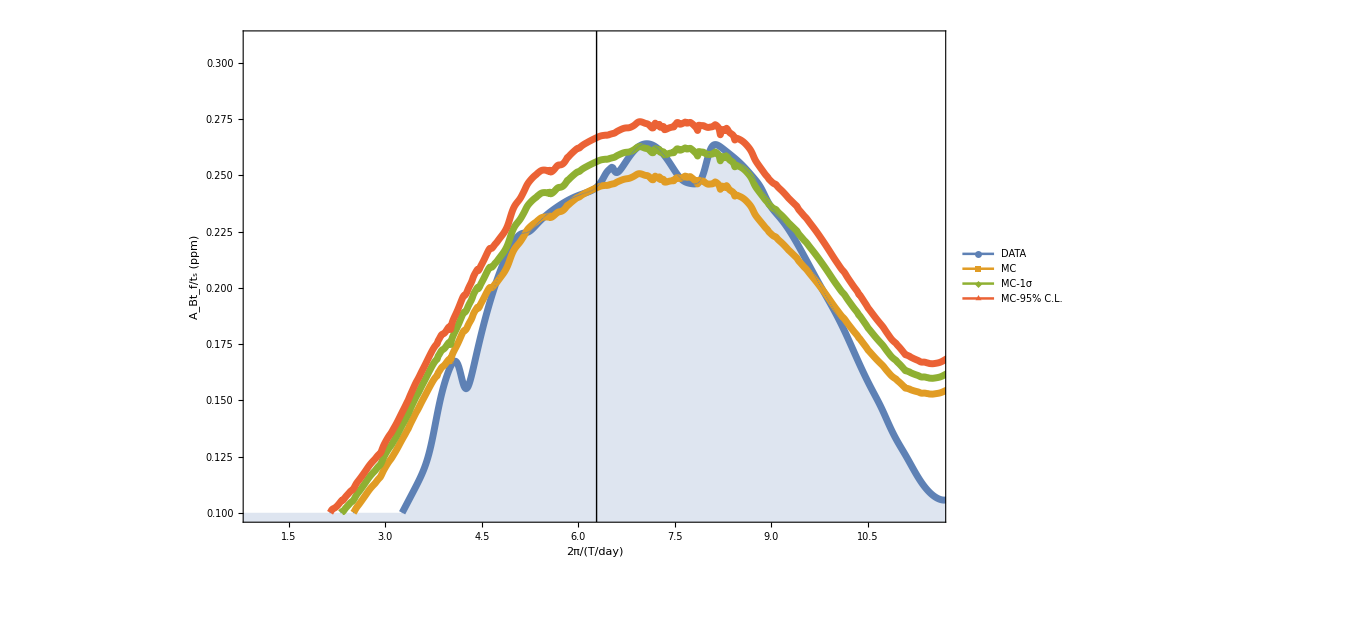

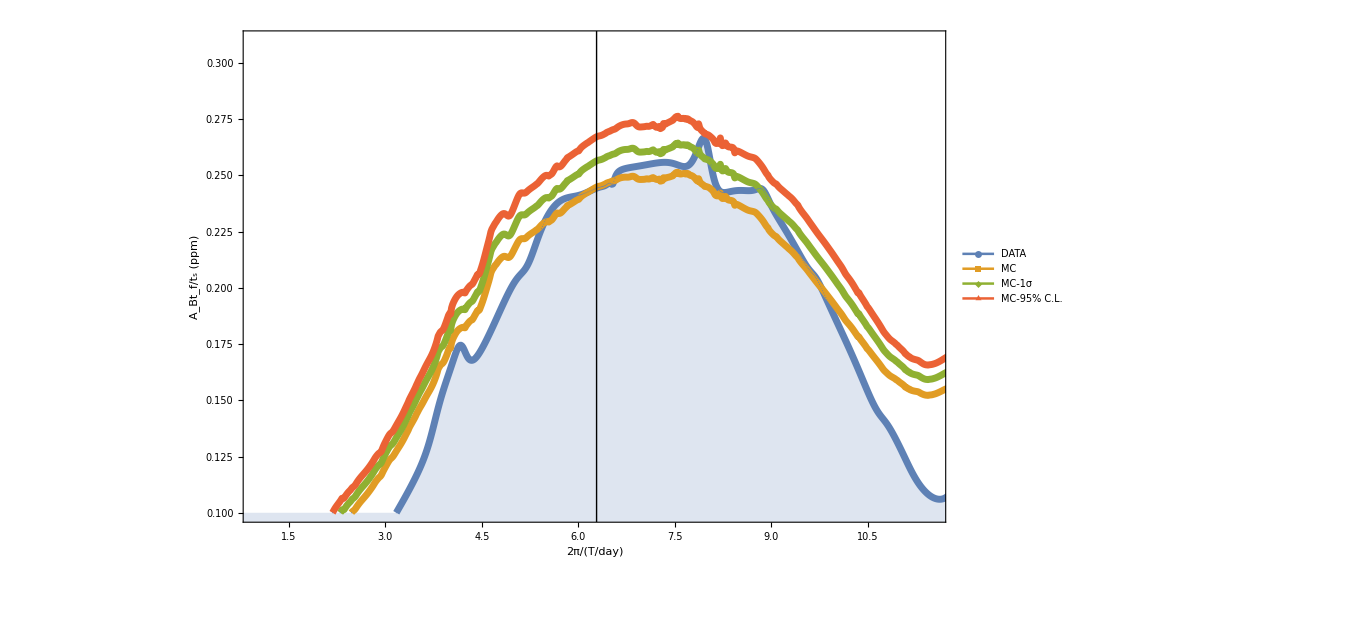

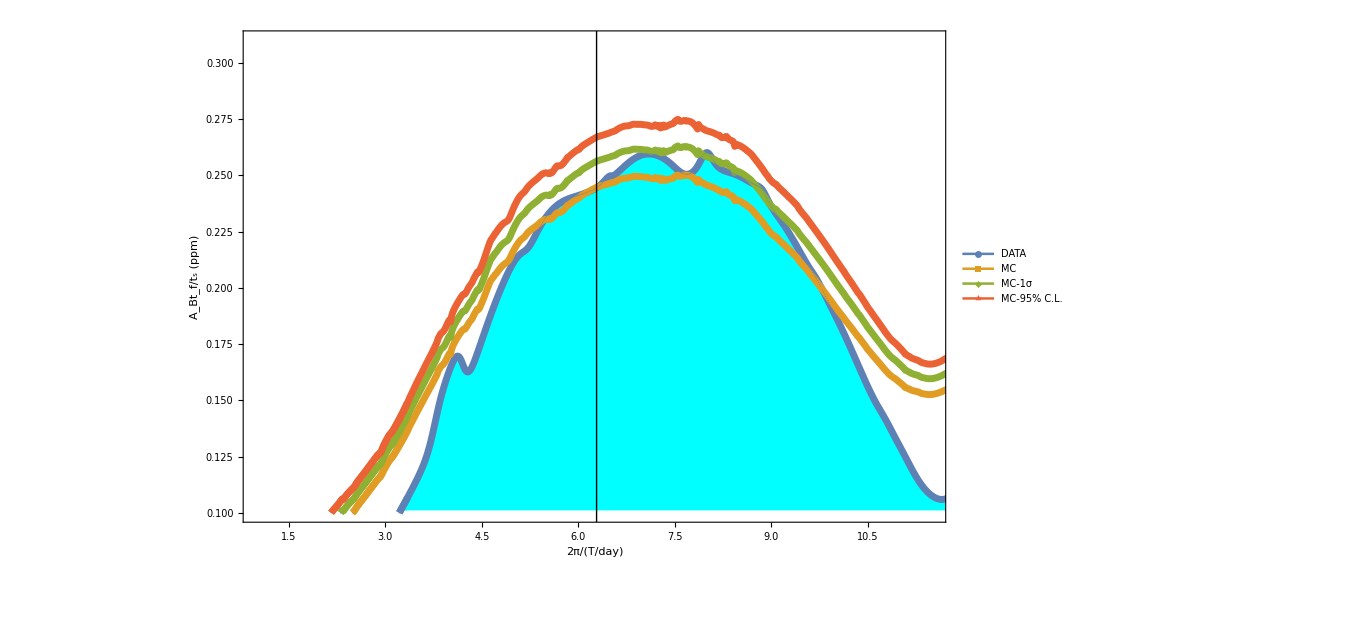

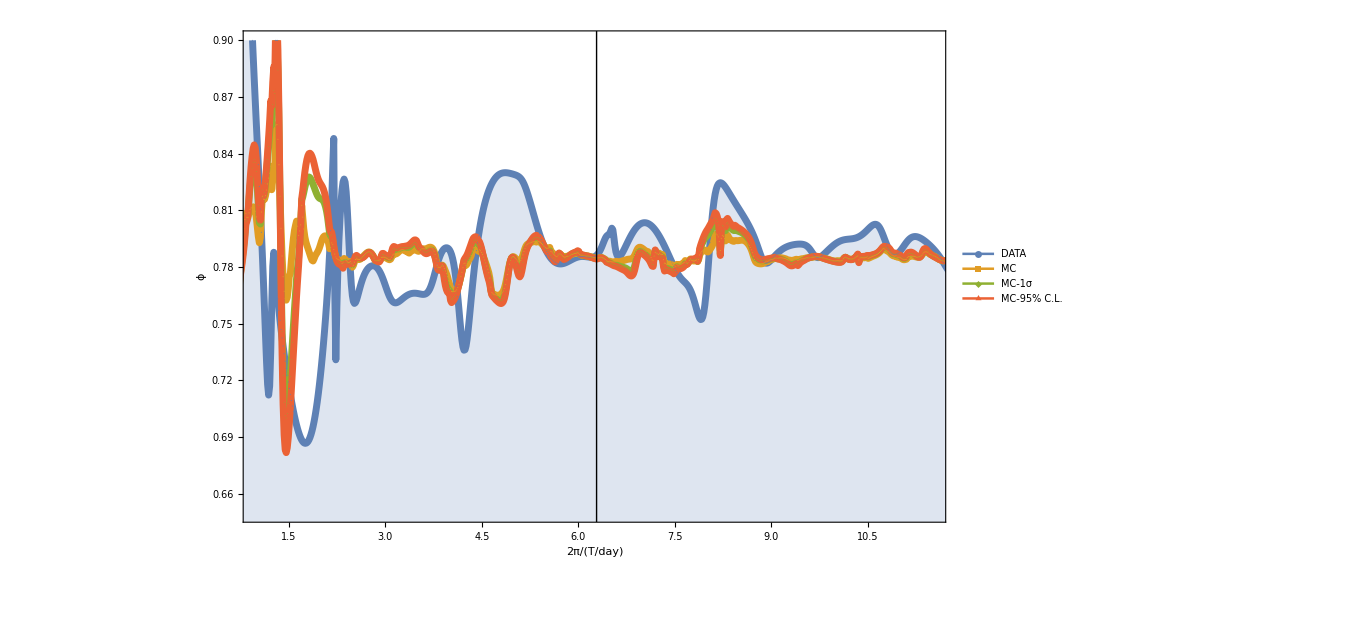

```mathematica
ListPlot[{ptgramfta,ptgramftamcm,ptgramftamcm1,ptgramftamcm95},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC-1σ","MC-95% C.L."},FrameLabel->{"2π/(T/day)","A_Bt_f/t_s (ppm)"},PlotMarkers->{Automatic,1},PlotRange->{{1,11.5},{.1,.31}},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1}]
ListPlot[{ptgramfta2,ptgramftamcm2,ptgramftamcm12,ptgramftamcm952},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC-1σ","MC-95% C.L."},FrameLabel->{"2π/(T/day)","A_Bt_f/t_s (ppm)"},PlotMarkers->{Automatic,1},PlotRange->{{1,11.5},{.1,.31}},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1}]
ListPlot[{Sqrt[ptgramfta^2+ptgramfta2^2]/Sqrt[2],Sqrt[ptgramftamcm^2+ptgramftamcm2^2]/Sqrt[2],Sqrt[ptgramftamcm1^2+ptgramftamcm12^2]/Sqrt[2],Sqrt[ptgramftamcm95^2+ptgramftamcm952^2]/Sqrt[2]},Filling->{1->Axis},FillingStyle->Cyan,Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC-1σ","MC-95% C.L."},FrameLabel->{"2π/(T/day)","A_Bt_f/t_s (ppm)"},PlotMarkers->{Automatic,1},PlotRange->{{1,11.5},{.1,.31}},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1}]
ListPlot[{ptgramftap,ptgramftamcmp,ptgramftamcm1p,ptgramftamcm95p},Filling->{1->0},Joined->True,PlotStyle->Thickness[.005],PlotLegends->{"DATA","MC","MC-1σ","MC-95% C.L."},FrameLabel->{"2π/(T/day)","ϕ"},PlotMarkers->{Automatic,1},PlotRange->{{1,11.5},{0.65,.9}},Frame->True,ImageSize->1000,FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],Epilog->{Directive[lineStyle],ln1}]
```

## Individual Fit

```mathematica
nlm10=NonlinearModelFit[Join[fta10,fta20],{aa Sin[2 Pi t+phi]+bb},{{aa,fta10[[1]][[2]]},{bb,fta10[[1]][[2]]},{phi,0}},t,Weights->Join[erra10,erra20],Method->NMinimize];
nlm10["ParameterTable"]
nlm10["BestFitParameters"][[;;,2]]
nlm10["ParameterErrors"]
nlm10["ANOVATable"]
nlm20=NonlinearModelFit[fta20,{aa Sin[ 2 Pi t+phi]+bb},{{aa,fta20[[1]][[2]]},{bb,fta20[[1]][[2]]},{phi,0}},t,Weights->erra20,Method->NMinimize];
nlm20["ParameterTable"]
nlm20["BestFitParameters"][[;;,2]]
nlm20["ParameterErrors"]
nlm20["ANOVATable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
aa | -0.400077 | 0.306102 | -1.307 | 0.19424
bb | -0.374984 | 0.221787 | -1.69074 | 0.0940321
phi | -0.621265 | 0.792261 | -0.784167 | 0.434815

{-0.400077,-0.374984,-0.621265}

{0.306102,0.221787,0.792261}

| DF | SS | MS
Model | 3 | 18.7106 | 6.23685
Error | 99 | 351.163 | 3.5471
Uncorrected Total | 102 | 369.874 | 
Corrected Total | 101 | 357.247 |

| Estimate | Standard Error | t-Statistic | P-Value
aa | -1.14123 | 0.608232 | -1.87631 | 0.0714619
bb | -0.134793 | 0.432614 | -0.311579 | 0.757754
phi | 1.45277 | 0.537887 | 2.70089 | 0.0117967

{-1.14123,-0.134793,1.45277}

{0.608232,0.432614,0.537887}

| DF | SS | MS
Model | 3 | 11.6434 | 3.88115
Error | 27 | 88.4714 | 3.27672
Uncorrected Total | 30 | 100.115 | 
Corrected Total | 29 | 100.008 |

## Test

```mathematica
tst=Table[Table[{10,k*l},{k,1,10}],{l,1,10}]
N[StandardDeviation[tst][[;;,2]]]
Mean[tst]
Mean[tst]-StandardDeviation[tst]
```

{{{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10}},{{10,2},{10,4},{10,6},{10,8},{10,10},{10,12},{10,14},{10,16},{10,18},{10,20}},{{10,3},{10,6},{10,9},{10,12},{10,15},{10,18},{10,21},{10,24},{10,27},{10,30}},{{10,4},{10,8},{10,12},{10,16},{10,20},{10,24},{10,28},{10,32},{10,36},{10,40}},{{10,5},{10,10},{10,15},{10,20},{10,25},{10,30},{10,35},{10,40},{10,45},{10,50}},{{10,6},{10,12},{10,18},{10,24},{10,30},{10,36},{10,42},{10,48},{10,54},{10,60}},{{10,7},{10,14},{10,21},{10,28},{10,35},{10,42},{10,49},{10,56},{10,63},{10,70}},{{10,8},{10,16},{10,24},{10,32},{10,40},{10,48},{10,56},{10,64},{10,72},{10,80}},{{10,9},{10,18},{10,27},{10,36},{10,45},{10,54},{10,63},{10,72},{10,81},{10,90}},{{10,10},{10,20},{10,30},{10,40},{10,50},{10,60},{10,70},{10,80},{10,90},{10,100}}}

{3.02765,6.0553,9.08295,12.1106,15.1383,18.1659,21.1936,24.2212,27.2489,30.2765}

{{10,11/2},{10,11},{10,33/2},{10,22},{10,55/2},{10,33},{10,77/2},{10,44},{10,99/2},{10,55}}

{{10,11/2-√(55/6)},{10,11-√(110/3)},{10,33/2-√(165/2)},{10,22-2 √(110/3)},{10,55/2-5 √(55/6)},{10,33-√330},{10,77/2-7 √(55/6)},{10,44-4 √(110/3)},{10,99/2-3 √(165/2)},{10,55-5 √(110/3)}}

```mathematica
For[i=1,i≤3,i++,
RandomSeed[CurrentDate[]];
Print[RandomVariate[NormalDistribution[totdat[[i]][[2]][[1]],totdat[[i]][[2]][[2]]]]];
]
```

0.958294

2.57176

0.0136103

```mathematica
Needs["SubKernels`RemoteKernels`"]
```

```mathematica
LaunchKernels[RemoteMachine["remote1.wolfram.com"]]
```

LaunchRemote::rsh: Command rsh remote1.wolfram.com -n -l tmpra "wolfram -wstp -linkmode Connect -linkprotocol TCPIP -linkname 58284@10.16.36.171,58285@10.16.36.171 -subkernel -noinit -nopaclet >& /dev/null &" may have failed (exit code 1).

General::time: Operation LaunchKernels timed out after 10. seconds.

$Failed

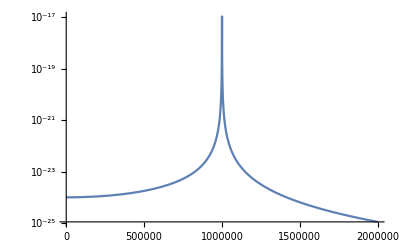

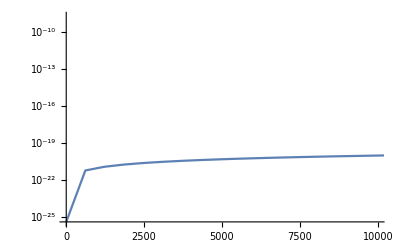

```mathematica
f[x_]:=(1)/((x^2-(10^6)^2)^2+1);
LogPlot[f[x],{x,0,2*10^6},PlotRange->Full]
LogPlot[NIntegrate[f[y],{y,0,x}],{x,0,2*10^6},PlotRange->{{0,10^4},Automatic}]
```